```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]]
Get["MagicSimulate`"]
Get["PedigreeOrigin`"]
```

D:\Chaozhi\GitHub Clones\RABBIT\RABBIT_Packages

```mathematica
(************************************************************************************************)
```

1

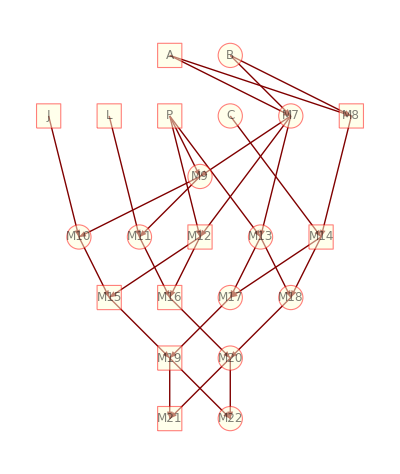

```mathematica
(*1: Pedigree of Native Americans; 
2: RIL by selfing;
3: RIL+ by selfing;
4: RIL by sibling*)
chooseped=RandomChoice[Range[4]]
Switch[chooseped,
1,
ped={{"Generation","MemberID","Gender",{"MotherID","FatherID"}},{0,"A",2,{0,0}},{0,"B",1,{0,0}},{1,"J",2,{0,0}},{1,"L",2,{0,0}},{1,"P",2,{0,0}},{1,"C",1,{0,0}},{1,"M7",1,{"B","A"}},{1,"M8",2,{"B","A"}},{2,"M9",1,{"M7","P"}},{3,"M10",1,{"M9","J"}},{3,"M11",1,{"M9","L"}},{3,"M12",2,{"M7","P"}},{3,"M13",1,{"M7","P"}},{3,"M14",2,{"C","M8"}},{4,"M15",2,{"M10","M12"}},{4,"M16",2,{"M11","M12"}},{4,"M17",1,{"M13","M14"}},{4,"M18",1,{"M13","M14"}},{5,"M19",2,{"M17","M15"}},{5,"M20",1,{"M18","M16"}},{6,"M21",2,{"M20","M19"}},{6,"M22",1,{"M20","M19"}}},
2,
nselfing=4;
mateScheme=Join[{"Pairing","Pairing","Pairing"},Table["Selfing",{nselfing}]];
nFounder=8;
ped=simPedigree[setIniPop[nFounder,False],mateScheme],
3,
nselfing=4;
mateScheme=Join[{"Pairing","Sibling","CrossPairing","Pairing"},Table["Selfing",{nselfing}]];
nFounder=8;
ped=simPedigree[setIniPop[nFounder,False],mateScheme],
4,
nsibling=5;
mateScheme=Join[{"Pairing","Pairing"},Table["Sibling",{nsibling}]];
nFounder=8;
ped=simPedigree[setIniPop[nFounder,False],mateScheme];
];
If[chooseped≠1,
nFounder=Count[ped[[All,-1]],{0,0}];
founderid=Take[CharacterRange["A","Z"],nFounder];
ped[[2;;,{2,4}]]=ped[[2;;,{2,4}]]/.Thread[Range[nFounder]->founderid];
(*"Female=1/Male=2/Hermaphrodite=0"*)
ped[[1,3]]="Gender"; 
];
pedigreePlot[ped,ImageSize->400,VertexLabeling->Automatic]
```

```mathematica
(************************************************************************************************)
```

```mathematica
nFounder=Count[ped[[All,-1]],{0,0}]
founderFGL=setfounderFGL[nFounder,True]
isautosome=True;
indlist=ped[[10;;,2]]
res=pedIdentityPrior[ped,founderFGL,isautosome,indlist];//AbsoluteTiming
res//MatrixForm
```

6

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6}}

{M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22}

{0.0777828,Null}

(Generation | MemberID | Gender | {MotherID,FatherID} | phi(11)_{aa}^mp | R_a^m | R_a^p | rho_{aa}^{mp} | J1112_{aa}^mp | J1121_{aa}^mp | J1122_{aa}^mp | J1211_{aa}^mp | J1213_{aa}^mp | J1222_{aa}^mp | J1232_{aa}^mp
2 | M9 | 1 | {M7,P} | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
3 | M10 | 1 | {M9,J} | 0. | 1.5 | 0. | 1.5 | 0. | 0. | 0. | 0. | 0. | 0. | 1.5
3 | M11 | 1 | {M9,L} | 0. | 1.5 | 0. | 1.5 | 0. | 0. | 0. | 0. | 0. | 0. | 1.5
3 | M12 | 2 | {M7,P} | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
3 | M13 | 1 | {M7,P} | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
3 | M14 | 2 | {C,M8} | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
4 | M15 | 2 | {M10,M12} | 0.1875 | 1.75 | 1.5 | 3.25 | 0.25 | 0.4375 | 0. | 0.25 | 1. | 0.4375 | 0.875
4 | M16 | 2 | {M11,M12} | 0.1875 | 1.75 | 1.5 | 3.25 | 0.25 | 0.4375 | 0. | 0.25 | 1. | 0.4375 | 0.875
4 | M17 | 1 | {M13,M14} | 0.125 | 1.5 | 1.5 | 3. | 0.25 | 0.25 | 0. | 0.25 | 1. | 0.25 | 1.
4 | M18 | 1 | {M13,M14} | 0.125 | 1.5 | 1.5 | 3. | 0.25 | 0.25 | 0. | 0.25 | 1. | 0.25 | 1.
5 | M19 | 2 | {M17,M15} | 0.1875 | 2.375 | 2.4375 | 4.8125 | 0.484375 | 0.445313 | 0. | 0.484375 | 1.46875 | 0.445313 | 1.48438
5 | M20 | 1 | {M18,M16} | 0.1875 | 2.375 | 2.4375 | 4.8125 | 0.484375 | 0.445313 | 0. | 0.484375 | 1.46875 | 0.445313 | 1.48438
6 | M21 | 2 | {M20,M19} | 0.234375 | 3.21875 | 3.21875 | 6.38672 | 0.697266 | 0.697266 | 0.0507813 | 0.697266 | 1.77344 | 0.697266 | 1.77344
6 | M22 | 1 | {M20,M19} | 0.234375 | 3.21875 | 3.21875 | 6.38672 | 0.697266 | 0.697266 | 0.0507813 | 0.697266 | 1.77344 | 0.697266 | 1.77344)

Calculate for the last pedigree member: {M22}

{0.503325,Null}

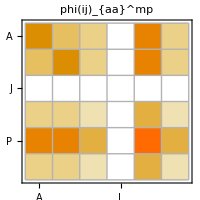
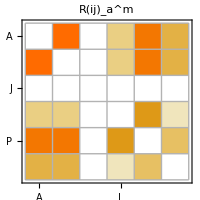
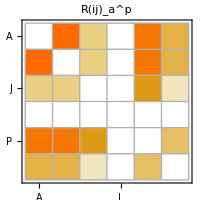
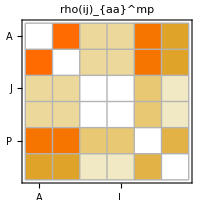
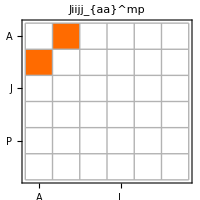

R(ij)_a^m=(0. | 0.3125 | 0. | 0.09375 | 0.289063 | 0.117188
0.3125 | 0. | 0. | 0.09375 | 0.289063 | 0.117188
0. | 0. | 0. | 0. | 0. | 0.
0.09375 | 0.09375 | 0. | 0. | 0.15625 | 0.03125
0.289063 | 0.289063 | 0. | 0.15625 | 0. | 0.109375
0.117188 | 0.117188 | 0. | 0.03125 | 0.109375 | 0.)

```mathematica
nFounder=Count[ped[[All,-1]],{0,0}];
founderFGL=setfounderFGL[nFounder,True];
isautosome=True;
indlist=ped[[-1;;,2]];
Print["Calculate for the last pedigree member: ",indlist];
res2=pedAncestryPrior[ped,founderFGL,isautosome,indlist];//AbsoluteTiming
xlab=Transpose[{Range[nFounder],ped[[2;;nFounder+1,2]]}];
Table[MatrixPlot[Normal[res2[[2,j]]],ImageSize->200,FrameTicks->{xlab,xlab},Mesh->All,MeshStyle->Directive[GrayLevel[0.7]],PlotLabel->res2[[1,j]]],{j,{7,8,9,10,13}}]
Print[res2[[1,8]],"=", res2[[2,8]]//MatrixForm]
```

```mathematica
res3=res2;
res3[[2,5;;]]=Total[Flatten[#]]&/@res2[[2,5;;]];
res3[[1,5;;]]=StringJoin["sum_",#]&/@res2[[1,5;;]];
Transpose[res3]//MatrixForm
Print["phi(11)_{aa}^mp =",phi11=Total[Diagonal[res2[[2,7]]]]]
phi11==res[[-1,5]]
res3[[2,8;;]]==res[[-1,6;;]]
```

(Generation | 6
MemberID | M22
Gender | 1
{MotherID,FatherID} | {M20,M19}
sum_f(i)_a^m | 1
sum_f(i)_a^p | 1
sum_phi(ij)_{aa}^mp | 1
sum_R(ij)_a^m | 3.21875
sum_R(ij)_a^p | 3.21875
sum_rho(ij)_{aa}^mp | 6.38672
sum_Jiiij_{aa}^mp | 0.697266
sum_Jiiji_{aa}^mp | 0.697266
sum_Jiijj_{aa}^mp | 0.0507813
sum_Jijii_{aa}^mp | 0.697266
sum_Jijik_{aa}^mp | 1.77344
sum_Jijjj_{aa}^mp | 0.697266
sum_Jijkj_{aa}^mp | 1.77344)

phi(11)_{aa}^mp =15/64

True

True